# Implementation of an Edmund Harriss-type Visualization

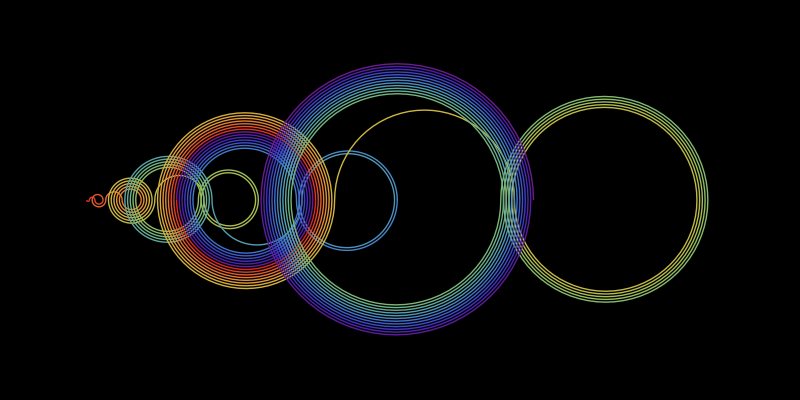

```mathematica
(* Generate the sequence *)
n=101;
recamanSequence=Module[{seq={0}},Do[Module[{prev,next},prev=Last[seq]-i;
next=Last[seq]+i;
If[prev>0&&!MemberQ[seq,prev],AppendTo[seq,prev],AppendTo[seq,next]]],{i,1,n-1}];
seq];
(* Produce graphics *)
plotRange={{-5,235},{-60,60}};
imageSize=800;
aspRat=(Ratios@Flatten[Differences/@ plotRange]);
cm=ColorData["Rainbow"];
cycles=2;
colorCycle= Function[{x}, Rcm[cycles * Mod[x, 1/cycles]]];
generateFrame[i_]:=Module[{center,r,arcs,startAngle,endAngle},arcs=Table[center=(recamanSequence[[j+1]]+recamanSequence[[j]])/2;
r=Abs[recamanSequence[[j+1]]-recamanSequence[[j]]]/2;
startAngle=If[EvenQ[j],0,Pi];
endAngle=If[EvenQ[j],Pi,2*Pi];
{colorCycle[j/n],{Circle[{center,0},r,{startAngle,endAngle}]}},{j,1,i}];
Graphics[{arcs},Background->Black,AspectRatio->aspRat,Axes->False,PlotRange->plotRange,ImageSize->imageSize]];
generateFrame[n-1]
```